```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
tk3[l_,u_,a_,b_,c_,d_,int_]:=Table[{j,Ceiling[j],{a,b}},{j,l,u,int}]~Join~Table[{j,"",{c,d}},{j,l+int/2,u-int/2,int}];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

# Papers: e.cm

## [1] On the Possibility of Electric Dipole Moments for Elementary Particles and Nuclei, E.M. Purcell, N.F. Ramsey, Phys.Rev. 78 (1950) 807-807. DOI: 10.1103/PhysRev.78.807. --- [2] Experimental limit to the electric dipole moment of the neutron, J.H. Smith, E.M. Purcell, N.F. Ramsey, Phys.Rev. 108 (1957) 120-122. DOI: 10.1103/PhysRev.108.120 [3] Limit to the Electric Dipole Moment of the Neutron, P.D. Miller, W.B. Dress, J.K. Baird, Norman F. Ramsey, Phys.Rev.Lett. 19 (1967) no.7, 381. DOI: 10.1103/PhysRevLett.19.381 [4] Upper Limit for the Electric Dipole Moment of the Neutron, W.B. Dress, J.K. Baird, P.D. Miller, Norman F. Ramsey, Phys.Rev. 170 (1968) no.5. DOI: 10.1103/PhysRev.170.1200 [6] Improved upper limit to the electric dipole moment of the neutron J.K. Baird, P.D. Miller, W.B. Dress, N.F. Ramsey, Phys.Rev. 179 (1969) 1285-1291. DOI: 10.1103/PhysRev.179.1285 [7] Improved upper limit for the electric dipole moment of the neutron, W.B. Dress, P.D. Miller, N.F. Ramsey, Phys.Rev. D7 (1973) 3147-3149. DOI: 10.1103/PhysRevD.7.3147 [8] Search for an Electric Dipole Moment of the Neutron, W.B. Dress, P.D. Miller, J.M. Pendlebury, Paul Perrin, Norman F. Ramsey, Phys.Rev. D15 (1977) 9. DOI: 10.1103/PhysRevD.15.9 --- [5] Search for a Neutron Electric Dipole Moment by a Scattering Experiment, C.G. Shull, R. Nathans, Phys.Rev.Lett. 19 (1967) 384-386. DOI: 10.1103/PhysRevLett.19.384 --- [6b] Electric dipole moment of the neutron, V.W. Cohen, R. Nathans, H.B. Silsbee, E. Lipworth, N.F. Ramsey, Phys.Rev. 177 (1969) 1942-1945. DOI: 10.1103/PhysRev.177.1942 --- [9] A search for the electric dipole moment of the neutron using ultracold neutrons, I.S. Altarev, Yu.V. Borisov, A.B. Brandin, A.I. Egorov, V.F. Ezhov, S.N. Ivanov, V.M. Lobashov, V.A. Nazarenko, G.D. Porsev, V.L. Ryabov et al., Nucl.Phys. A341 (1980) 269-283. DOI: 10.1016/0375-9474(80)90313-9 [10] A New Upper Limit on the Electric Dipole Moment of the Neutron, I.S. Altarev, Yu.V. Borisov, N.V. Borovikova, A.B. Brandin, A.I. Egorov, V.F. Ezhov, S.N. Ivanov (St. Petersburg, INP), V.M. Lobashev, V.A. Nazarenko, V.L. Ryabov et al., Phys.Lett. 102B (1981) 13-16. DOI: 10.1016/0370-2693(81)90202-1 [11] New measurement of the electric dipole moment of the neutron, I.S. Altarev, Yu.V. Borisov, N.V. Borovikova, S.N. Ivanov, E.A. Kolomensky, M.S. Lasakov, V.M. Lobashev, V.A. Nazarenko, A.N. Pirozhkov, A.P. Serebrov et al., Phys.Lett. B276 (1992) 242-246. DOI: 10.1016/0370-2693(92)90571-K --- [12] Search for a Neutron Electric Dipole Moment, J.M. Pendlebury, K.F. Smith, R. Golub, J. Byrne, Phys.Lett. 136B (1984) 327-330. DOI: 10.1016/0370-2693(84)92013-6 [13] A Search for the Electric Dipole Moment of the Neutron, K.F. Smith, N. Crampin, J.M. Pendlebury, D.J. Richardson, D. Shiers, K. Green, A.I. Kilvington, J. Moir, H.B. Prosper, D. Thompson et al., Phys.Lett. B234 (1990) 191-196. DOI: 10.1016/0370-2693(90)92027-G [14] New experimental limit on the electric dipole moment of the neutron, P.G. Harris, C.A. Baker, K. Green, P. Iaydjiev, S. Ivanov (Rutherford), D.J.R. May, J.M. Pendlebury, D. Shiers, K.F. Smith, M. van der Grinten et al., Phys.Rev.Lett. 82 (1999) 904-907. DOI: 10.1103/PhysRevLett.82.904 [15] An Improved experimental limit on the electric dipole moment of the neutron, C.A. Baker, D.D. Doyle, P. Geltenbort, K. Green, M.G.D. van der Grinten, P.G. Harris, P. Iaydjiev, S.N. Ivanov, D.J.R. May, J.M. Pendlebury et al., Phys.Rev.Lett. 97 (2006) 131801. DOI: 10.1103/PhysRevLett.97.131801. arXiv: hep-ex/0602020 --- [16] Revised experimental upper limit on the electric dipole moment of the neutron, J. M. Pendlebury, S. Afach, N.J. Ayres, C.A. Baker, G. Ban, G. Bison, K. Bodek, M. Burghoff, P. Geltenbort, K. Green et al., Phys.Rev. D92 (2015) no.9, 092003. DOI: 10.1103/PhysRevD.92.092003

### [1] [2][3][4][6][7][8]: ORNL [5][6b]: BNL [9][10][11]: LNPI [12][13][14]: RAL-Sussex-ILL [15][16]: Sussex-ILL-PSI

## [1] 06.1950; <3E-18 --- [2] 10.1957; (.1±2.4)E-20 [3] 08.1967; (2±3)E-22 [4] 06.1968; (-0.3±0.8)E-22, 3E-22 [6] 03.1969; (1.54±1.12)E-23, 5E-23 [7] 01.1973; (3.2±7.5)E-24, 1E-23 [8] 06.1977; (0.4±1.5)E-24, 3E-24 --- [5] 08.1967; (2.4±3.9)E-22 --- [6b] 01.1969; -, 1E-21 --- [9] 06.1980; (4±7.55)E-25, 1.6E-24 [10] 06.1981; (2.1±2.4)E-25, (2.3±2.3)E-25 (combining with before), 6E-25 [11] 02.1992; (2.6±4.2±1.6)E-26, 1.1E-25 --- [12] 03.1984; (+0.3 ± 4.8)E-25 [13] 01.1990; −(3±5)E-25 [14] 02.1999; (1.0±3.6)E-26, 6.3E-26 --- [15] 09.2006; (0.2±1.5±0.7)E-26, 2.9E-26 [16] 11.2015; (0.21±1.82)E-26, 3E-26

```mathematica
thk=.002;
acdat={
{
{N[1950+(6/12)],PlusMinus[.1,3]*10^(-18)}
},
{
{N[1957+(10/12)],PlusMinus[.1,2.4]*10^(-20)},
{N[1967+(8/12)],PlusMinus[2,3]*10^(-22)},
{N[1968+(8/12)],PlusMinus[.3,.8]*10^(-22)},
{N[1969+(3/12)],PlusMinus[1.54,1.12]*10^(-23)},
{N[1973+(1/12)],PlusMinus[3.2,7.5]*10^(-23)},
{N[1977+(6/12)],PlusMinus[0.4,1.5]*10^(-24)}
},
{
{N[1967+(8/12)],PlusMinus[2.4,3.9]*10^(-22)}
},
{
{N[1969+(1/12)],PlusMinus[0,1]*10^(-21)}
},
{
{N[1980+(6/12)],PlusMinus[4,7.55]*10^(-25)},
{N[1981+(6/12)],PlusMinus[2.1,2.4]*10^(-25)},
{N[1992+(2/12)],PlusMinus[2.6,Sqrt[4.2^2+1.6^2]]*10^(-25)}
},
{
{N[1984+(3/12)],PlusMinus[0.3,4.8]*10^(-25)},
{N[1990+(1/12)],PlusMinus[3,5]*10^(-25)},
{N[1999+(2/12)],PlusMinus[1,3.6]*10^(-26)}
},
{
{N[2015+(6/12)],PlusMinus[.21,1.82]*10^(-26)}
}
};
pttab=Table[Transpose[{acdat[[k]][[;;,1]],Transpose[{acdat[[k]][[;;,2]][[;;,1]],acdat[[k]][[;;,2]][[;;,2]]}]}],{k,1,Dimensions[acdat][[1]]}];
ptsty=-27;pteny=4;ptinty=3;numpart=Dimensions[pttab][[1]];
gridln={Table[k,{k,1,numpart,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
(*cht=EDAListPlot[pttab,PlotRange->{{1940,2020},Full},Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"Time (year)","<d^(meas)(90% C.L.) e.cm"},LabelStyle->{26,Black,Bold},TicksStyle->{Directive[FontSize->26]},GridLines->Automatic,
FrameTicks->{(*y,x*){tk2[ptsty,pteny,.02,0,0,0,ptinty],tk2[ptsty,pteny,.02,0,0,0,ptinty]},{tk3[1940,2010,.02,0,0,0,3],None}},AspectRatio->.4,ImageSize->1200]*)
```

{{1957.83,1.×10^-21,2.4×10^-20},{1967.67,2.×10^-22,3.×10^-22},{1968.67,3.×10^-23,8.×10^-23},{1969.25,1.5×10^-23,1.1×10^-23},{1973.08,3.2×10^-23,7.5×10^-23},{1977.5,4.×10^-25,1.5×10^-24}}

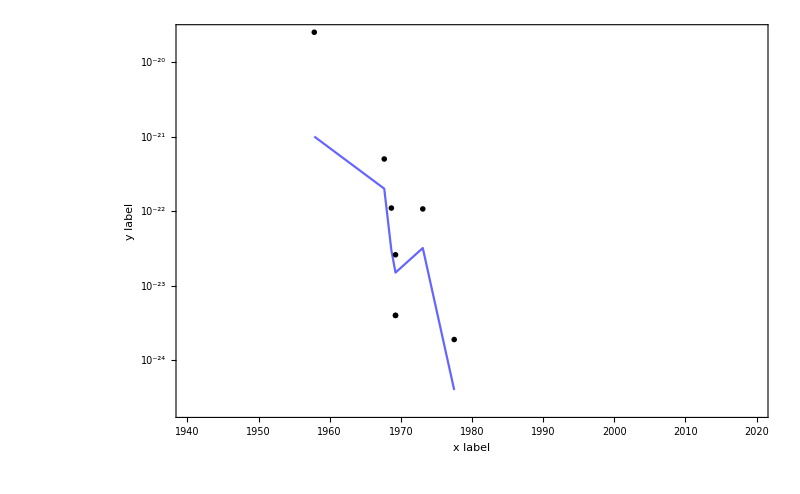

```mathematica
Options[errListPlot]={Filling->{1->{2}},Joined->{False,False,True},PlotStyle->{Black,Black,Directive[Opacity[0.6],Blue]},FillingStyle->Black,PlotMarkers->{Graphics@Line[.04 {{-1,0},{1,0}}],Graphics@Line[.04 {{-1,0},{1,0}}],""}};
errListPlot[plotFun_,data_,opts:OptionsPattern[]]:=Block[{},plotFun[{{#[[1]],#[[2]]-#[[3]]}&/@data,{#[[1]],#[[2]]+#[[3]]}&/@data,data[[;;,{1,2}]]},opts,Sequence@@Options[errListPlot]]]
datatst=Transpose[{acdat[[2]][[;;,1]],acdat[[2]][[;;,2]][[;;,1]],acdat[[2]][[;;,2]][[;;,2]]}]
errListPlot[ListLogPlot,datatst,PlotRange->{{1940,2020},Full},Frame->True,FrameLabel->{"x label","y label"},ImageSize->800,BaseStyle->{18,FontFamily->"Arial"}]
```

```mathematica
Export[StringJoin[PicDir,seperator,"EDM_time.png"],cht]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_all.png